```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/quantum_stochastic/math

```mathematica
MiyamotoData=Import["NTot_2pathsFromRandomNbk_1e7path.csv"];//AbsoluteTiming
```

{58.7958,Null}

```mathematica
err=10^-4;
sample=10^4;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
Length[dN2vsNb]
```

10000

```mathematica
NbList=dN2vsNb[[All,1]];
```

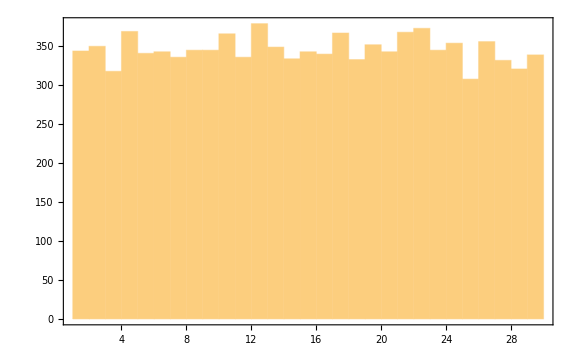

```mathematica
Histogram[NbList]
```

```mathematica
dN=1;
Nbmin=2;
Nmax=29;
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.198073,Null}

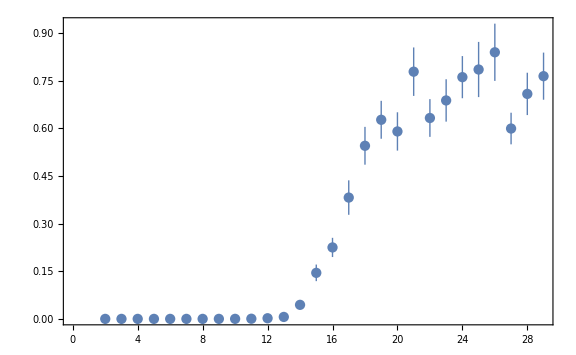

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.090569,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
Integrate[Exp[a0 LegendreP[0,x]+a1 LegendreP[1,x]-a2 LegendreP[2,x]],x]
```

(ⅇ^(a0+a1^2/(6 a2)+a2/2) √(π/6) Erf[(-a1+3 a2 x)/(√6 √a2)])/(√a2)

```mathematica
f[x_]=c/(1+Exp[-a0 LegendreP[0,x]-a1 LegendreP[1,x](*-a2 LegendreP[2,x]-a3 LegendreP[3,x]-a4 LegendreP[4,x]-a5 LegendreP[5,x]*)]);
g[x_]=a0 LegendreP[0,x]+a1 LegendreP[1,x]+a2 LegendreP[2,x]+a3 LegendreP[3,x]+a4 LegendreP[4,x]+a5 LegendreP[5,x];
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])

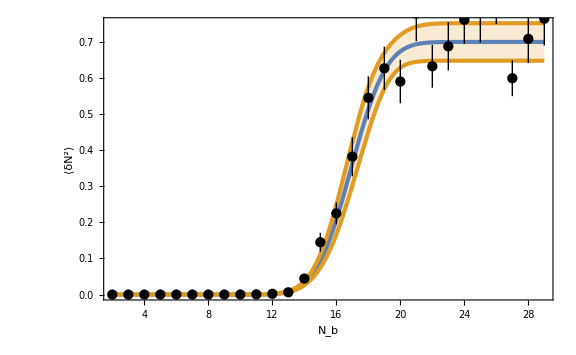

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

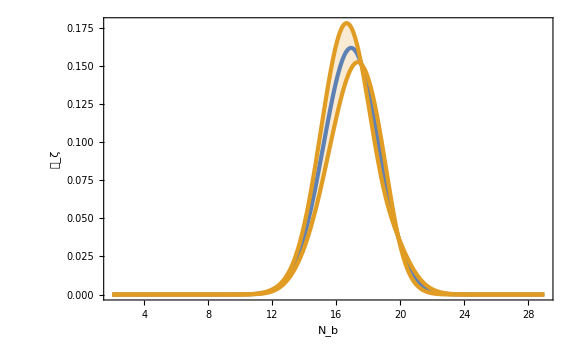

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],Subscript[𝒫, ζ]}]
```

### N = 1e4

```mathematica
sample=10^4;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.173284,Null}

```mathematica
ListPlot[dN2List,Joined->False]
```

-Graphics-

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.08617,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.350062 (1.00012+Erf[0.409478 (-16.9263+x)])

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

-Graphics-

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```

-Graphics-

### N = 1e5

```mathematica
sample=10^5;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.699842,Null}

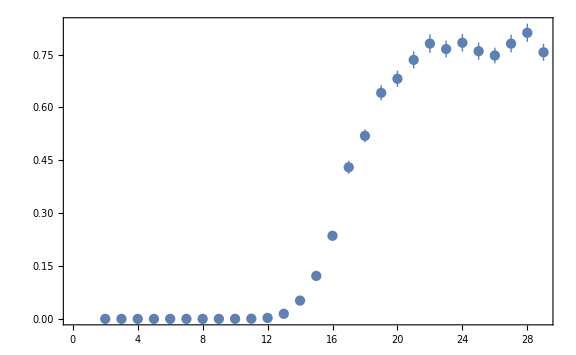

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{0.774621,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.380373 (0.999992+Erf[0.38106 (-16.8998+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.380373 (0.999992+Erf[0.38106 (-16.8998+x)])

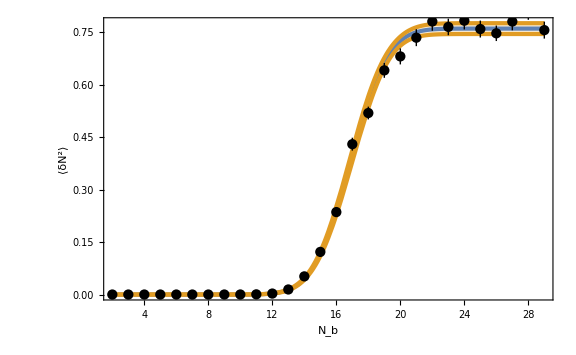

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

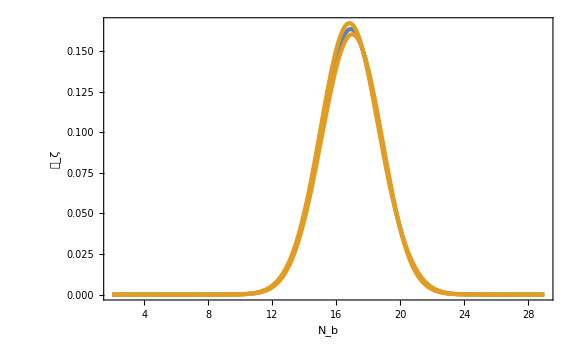

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```

### N = 1e6

```mathematica
sample=10^6;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{5.54572,Null}

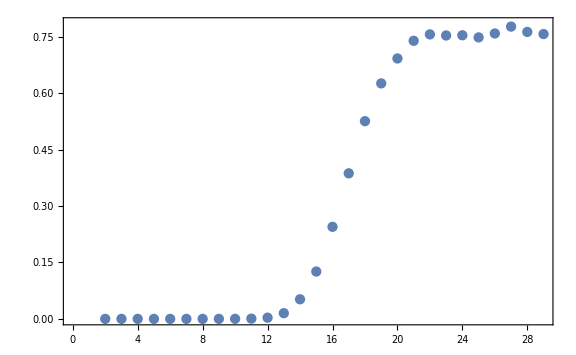

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{5.52411,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.377094 (0.999939+Erf[0.366619 (-16.9312+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.377094 (0.999939+Erf[0.366619 (-16.9312+x)])

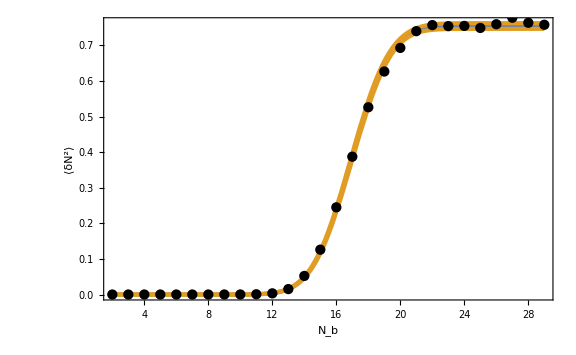

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

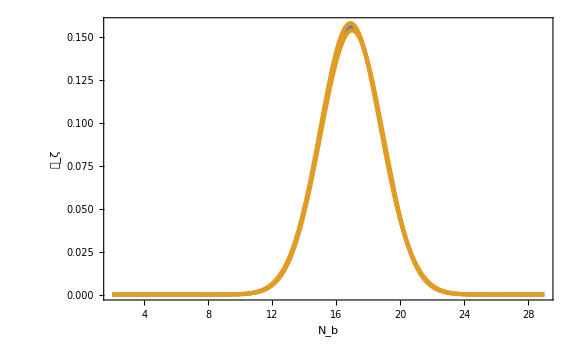

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```

### N = 1e7

```mathematica
sample=10^7;
```

```mathematica
dN2vsNb=Map[{#[[1]],(#[[2]]-#[[3]])^2/2}&,MiyamotoData[[2;;1+sample]]];
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=ParallelTable[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err],0]},{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{57.1784,Null}

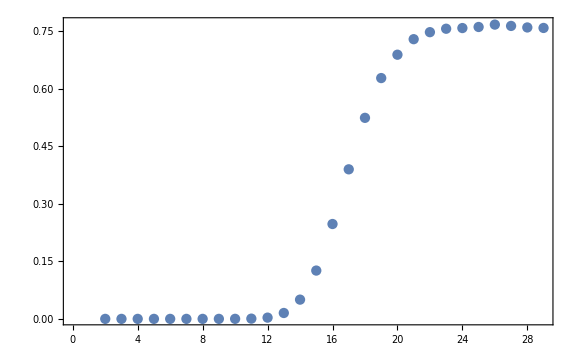

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=ParallelTable[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],err]},None],{Nb,Nbmin,Nmax,dN}];//AbsoluteTiming
```

{59.8831,Null}

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
h[x_]=a0 (Erf[a1(x-a2)]+a3);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],(*f[x]*)(*g[x]*)h[x],{a0,a1,a2,a3(*,a4,a5*)(*,c*)},x,Weights->weights,MaxIterations->100000]
```

FittedModel[0.376939 (0.999692+Erf[0.363006 (-16.9355+x)])]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.376939 (0.999692+Erf[0.363006 (-16.9355+x)])

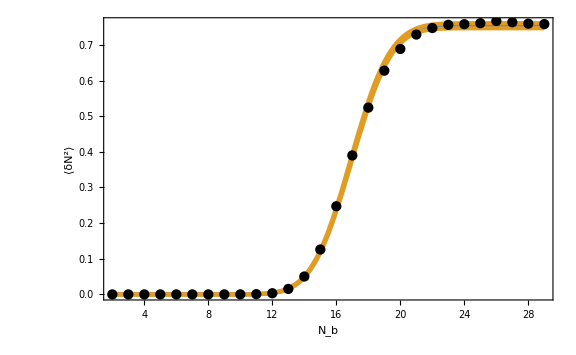

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},FrameLabel->{{"⟨δN^2⟩",None},{Subscript[N, "b"],𝒩==sample}}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

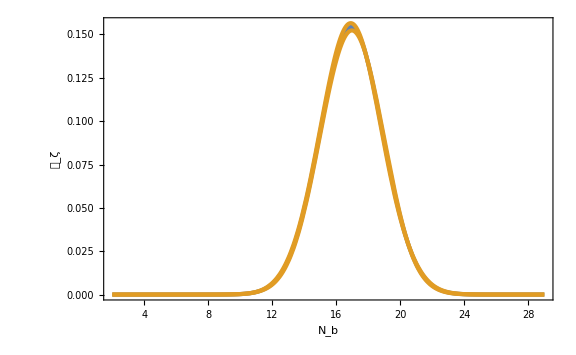

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{{Subscript[𝒫, ζ],None},{Subscript[N, "b"],𝒩==sample}}]
```